## Modelling Practice --对于动物体重和心率关系的建模

### 建模假设 Assumption：

1. 哺乳动物身体化学成分相似，即密度ρ相同。

2. 单位时间散失热量与该物种皮肤面积成正比，Q ∝ S。

3. 哺乳动物心室容积和该哺乳动物体积成正比，即 V_0 ∝ V。

4. 单位体积血液携带能量相同，为 D。

### 模型建立 Construction：

首先，W=ρV，对于所有物种，该种动物体重为该种动物身体密度和体积的乘积。
设存在某一线度r描述该种动物大小，则应有 V ∝ r^3，S ∝ r^2。单位时间散失热量与该物种皮肤面积成正比，即 Q ∝ S。
单位时间散热量和等于单位时间通过该种动物表面皮肤的血流量 δ 与单位体积血液携带能量D之积，即 Q = δ D。而血流量等于心跳频率 n 和每次心跳泵血体积即心室体积 V_0 的乘积，δ = V_0 n。
由上述关系可推出 n W ∝ S，即 n W^(1/3) = C，其中C为某一常数。

### 模型求解 Solution：

```mathematica
weights = {25,200,2000,5000,30000,50000,70000,450000};
rates = {670,420,205,120,85,70,72,38};
products = weights^(1/3)*rates;
```

下图为常数C随不同物种的变化情况

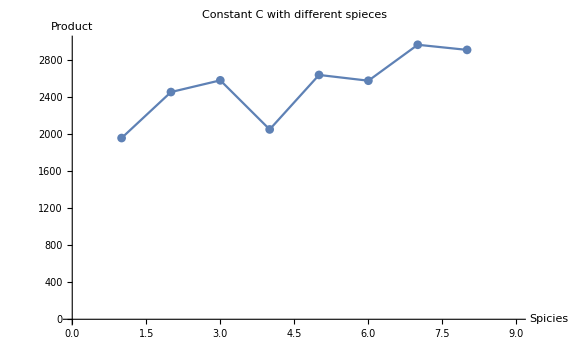

```mathematica
ListPlot[products,Joined->True,PlotMarkers->Automatic,PlotRange->{{0,9},{0,3000}},PlotLabel->"Constant C with different spieces",AxesLabel->{"Spicies","Product"},LabelStyle->{FontFamily->"Microsoft YaHei UI",GrayLevel[0],Italic},ImageSize->Large]
```

下图为常数C的对数随不同物种的变化情况

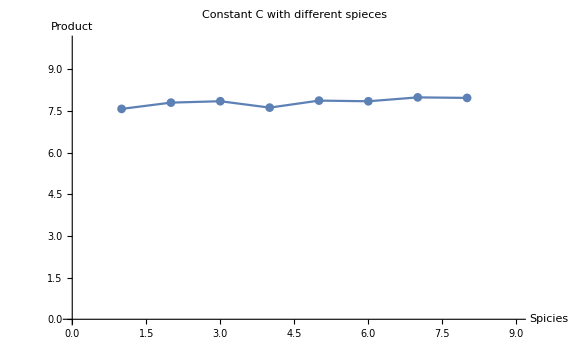

```mathematica
ListPlot[Log[products],Joined->True,PlotMarkers->Automatic,PlotRange->{{0,9},{0,10}},PlotLabel->"Constant C with different spieces",AxesLabel->{"Spicies","Product"},LabelStyle->{FontFamily->"Microsoft YaHei UI",GrayLevel[0],Italic},ImageSize->Large]
```

### 模型检验 Validation：

```mathematica
N[Mean[products]]
```

2518.67

```mathematica
N[StandardDeviation[products]]
```

361.259

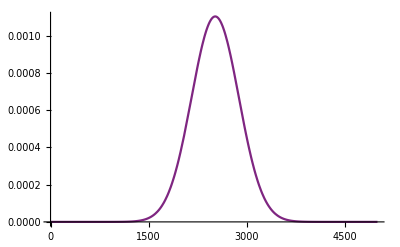

```mathematica
Plot[PDF[NormalDistribution[%81,%82],x],{x,0,5000},PlotRange->All,ColorFunction->"Rainbow"]
```

模型较为粗糙，但是总体正确反映了变量的关系。其标准差与平均值比值较大，可靠程度低。需要进一步完善。